5.4

3.5

(0 | 1
2 | 1)

(0 | 0
1. | 0)

(k1 | k2
k1 | k2)

(0 | 0
1. k1 | 1. k2)

(s | -1
-2-1. k1 | -1-1. k2+s)

-2-1. k1-s-1. k2 s+s^2

1.54286

{-2-1. k1,-1-1. k2,1}

{-2-1. k1,-1-1. k2,1}=={2.38041,1.54286,1}

{{k1→-4.38041,k2→-2.54286}}

(-4.38041
-2.54286)

s==-0.771429-1.33615 ⅈ||s==-0.771429+1.33615 ⅈ

(0 | 1
-2.38041 | -1.54286)

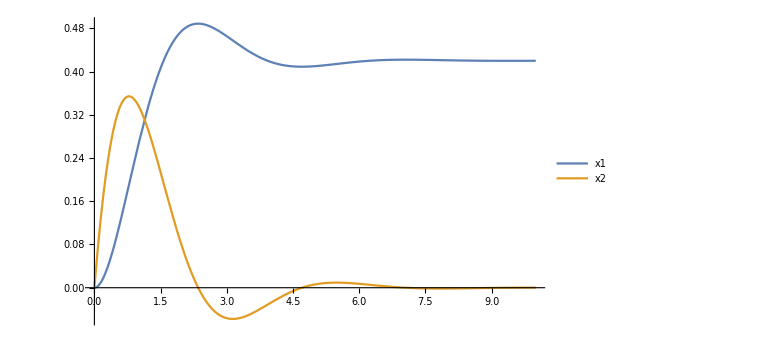

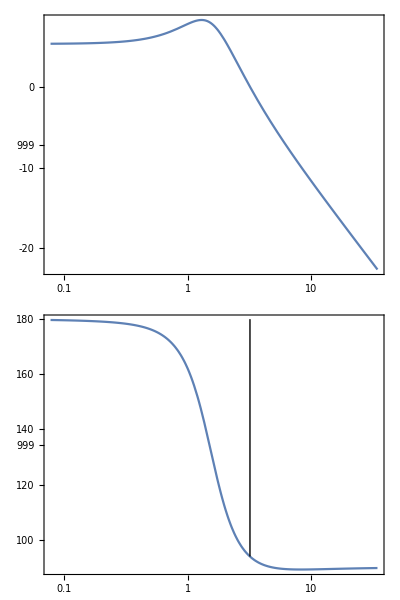

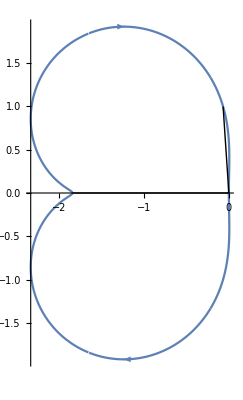

```mathematica
ab = {1,1,1};
A = {{0,1},{2,1}};
Id = IdentityMatrix[2];
B = {{0,0},{1.,0}};
K = {{k1,k2},{k1,k2}};
Tau = 5.4
Tpz = 3.5
A//MatrixForm
B//MatrixForm
K//MatrixForm
B.K//MatrixForm
Id*s - A - B.K//MatrixForm
Xseq = Det[ Id*s - A - B.K]
W = Tau/Tpz
Coef = CoefficientList[Xseq ,s] 
lsys = (Coef == {W^2*ab[[3]],W*ab[[2]],ab[[1]]})
sol = Solve[lsys,{k1,k2}]
k1S = sol[[1]][[1]][[2]];
k2S = sol[[1]][[2]][[2]];
Ks = {k1S,k2S};
Ks//MatrixForm
(*-2-k1+(-1-k2) s+s^2*)
Roots[-2-k1S+(-1-k2S) s+s^2==0,s]
A[[2]][[1]]= -(-2-k1S);
A[[2]][[2]]= -(-1-k2S);
A//MatrixForm
SS= StateSpaceModel[{A,Transpose[{B[[ All, 1]]}], {Ks}}];
Tf = TransferFunctionModel[SS,s];
PP = StateResponse[SS,{UnitStep[t]},{t,0,10}]; 
PPtf = OutputResponse[Tf,{UnitStep[t]},{t,0,10}]; 
Plot[PP,{t,0,10},PlotRange->Full, ImageSize->Large, PlotLegends->{"x1","x2"}] (*графік ПП*)
gpm=GainPhaseMargins[Tf];
BodePlot[Tf, StabilityMargins->gpm]
NyquistPlot[Tf, StabilityMargins->gpm]
```